```mathematica
SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

Global`

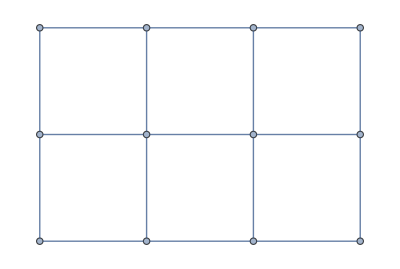

```mathematica
g = System`GridGraph[{3,4}]
```

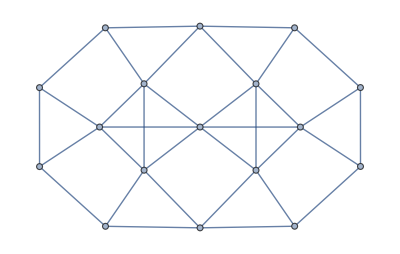

```mathematica
System`LineGraph[g]
```

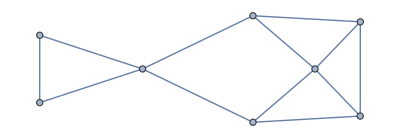
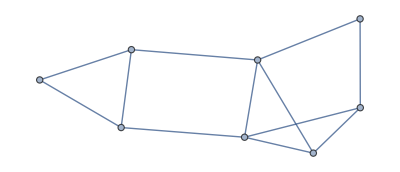
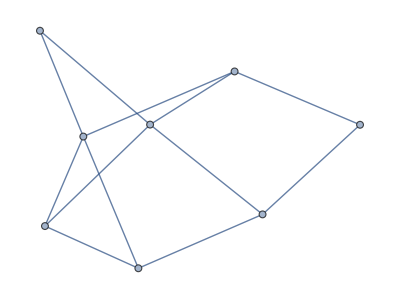

```mathematica
System`RandomGraph[DegreeGraphDistribution[{3,4,2,3,3,4,2,3}],3]
```

```mathematica
(*Neighbors[i_,j_, m_,n_,dist_] := Select[Complement[Flatten[Table[{i+di, i+dj},{di,-dist,dist},{dj,-dist,dist}],1],{{i,j}}],
1<=First[#]<=5 && 1≤Last[#]≤4 &]*)
```

{{1,9},{1,10},{2,9},{2,6},{3,6},{3,10},{4,6},{5,7},{5,9},{6,9},{6,12},{7,11},{7,1},{8,10},{8,14},{9,10},{9,11},{10,13},{11,16},{11,15},{12,11},{12,10},{13,7},{14,7},{14,12},{15,10},{15,9},{16,6},{16,12}}

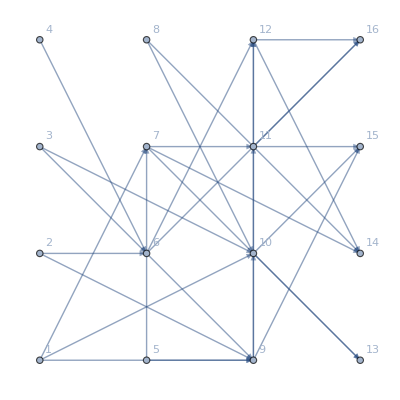

```mathematica
m=4;
n=4;
maxDist = 2;
maxDegree = 2;
vlist = Range[1,m*n];
vcoords= Flatten[Table[{i,j},{i,1,m},{j,1,n}],1];
elist = {};
Vertex1D[ij_,m_,n_] := (First[ij]-1)*n+Last[ij]
Neighbors[i_,j_, m_,n_,dist_] := Select[Flatten[Table[{i+di, j+dj},{di,-dist,dist},{dj,-dist,dist}],1],
1<=First[#]≤m && 1≤Last[#]≤n && #≠{i,j}&]
Do[With[{newE = {Vertex1D[{i,j},m,n],Vertex1D[adj,m,n]}},
AppendTo[elist,newE]],{i,1,m},{j,1,n},{adj, RandomChoice[Neighbors[i,j,m,n,maxDist],maxDegree]}]
elist =DeleteDuplicates[elist,#1==#2||#1==Reverse[#2]& ]
newG=System`Graph[vlist,elist,VertexCoordinates->vcoords,
System`VertexWeight->Table[1/Length[vlist], Length[vlist]],System`EdgeWeight-> Table[1,Length[elist]],
System`VertexLabels->Automatic,
System`EdgeStyle->Directive[Opacity[0.5], Thick], EdgeShapeFunction->"Arrow"];
newG = UndirectedGraph[newG]
(*Map[#->PropertyValue[{g,#}]]*)
```

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

Table::iterb: Iterator {j,RandomChoice[Select[Range[i+1,m n],0<VertexDistance[i,#1,m,n]≤4&],RandomInteger[{0,2}]]} does not have appropriate bounds.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

Table::iterb: Iterator {j,RandomChoice[Select[Range[i+1,m n],0<VertexDistance[i,#1,m,n]≤4&],RandomInteger[{0,2}]]} does not have appropriate bounds.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

Table::iterb: Iterator {j,RandomChoice[Select[Range[i+1,m n],0<VertexDistance[i,#1,m,n]≤4&],RandomInteger[{0,2}]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

Table::iterb: Iterator {j,RandomChoice[Select[Range[i+1,m n],0<VertexDistance[i,#1,m,n]≤4&],RandomInteger[{0,2}]]} does not have appropriate bounds.

EdgeAdd::inv: The argument Table[i<->j,{i,1,8},{j,RandomChoice[Select[Range[i+1,m n],0<VertexDistance[i,Slot[«1»],m,n]≤4&],RandomInteger[{0,2}]]}] in EdgeAdd[Graph[<9>, <12>], Table[i <-> j, {i, 1, 8}, {j, RandomChoice[Select[Range[Plus[<<2>>], Times[<<2>>]], Inequality[<<5>>] & ], RandomInteger[{0, 2}]]}]] is not a valid edge.

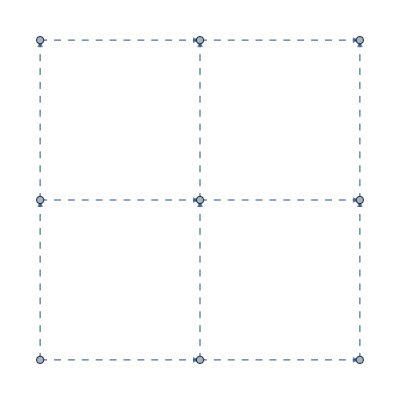
EdgeAdd[-Graphics-,Table[i<->j,{i,1,8},{j,RandomChoice[Select[Range[i+1,m n],0<VertexDistance[i,#1,m,n]≤4&],RandomInteger[{0,2}]]}]]

{2,3,2,3,4,3,2,3,2}

```mathematica
m=3;n=3;
g= System`GridGraph[{m,n},System`EdgeStyle->Directive[Dashed,Thick], EdgeShapeFunction->"Arrow"];newE = Flatten[Table[UndirectedEdge[i,j],{i,1,m*n-1},
{j, RandomChoice[
Select[Range[i+1,m*n],0<VertexDistance[i,#,m,n]≤4&]
,RandomInteger[{0,2}]]}],1];
System`EdgeAdd[g,newE]
VertexDegree[g]
```

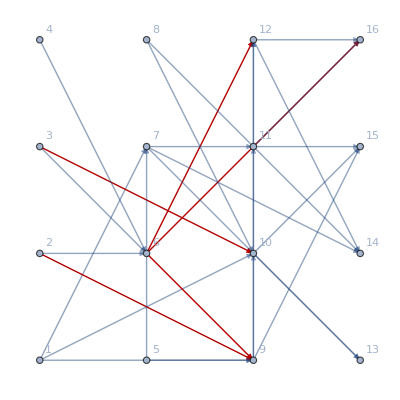

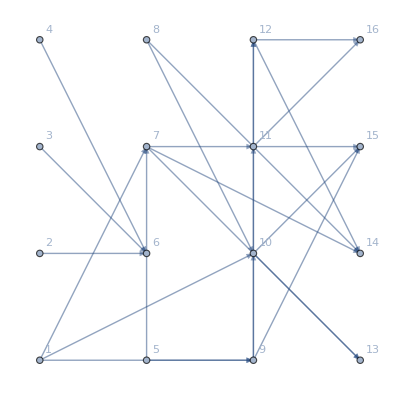

```mathematica
ShowSpectralCut[newG]
SpectralCut[newG]
```